For An :
1.)  calculate the volume of air cleaned by the screen as a function of V_robot,horizontal, θ, and s  (fix s< r?)
2.) find exponential fit to mosquito density as function of height
3.) combine 1 and 2 -- what is the optimal configuration
4.)  velocity down is not a constant.... can we make a better
do your best

## OptimizeMosquitoDroneConfiguration.nb Mosquito Eliminating Screens Aaron T. Becker Simulates different arrangements of mosquito screens and examines how well they work.

Assume the drone is a square, with each side 2 RadRob. 
To hover, the drone must push air down with velocity velocity_down to apply a force that cancels the pull of gravity. The drone has mass mRob.  
mRob *g = massFlow*velocity_down
mass * gravity = (density air * Area_robotCrossSection* velocity_down)*velocity_down
kg  *m/s^2= (kg/m^3*m^2*m/s)*m/s
the units work!
velocity_down = √((mass * gravity)/(density air * Area_robotCrossSection))

```mathematica
mRob = 2 ; (* kg, https://3dr.com/solo-gopro-drone-specs/*)
densityAir = 1.225; (* kg/m3, Air density,like air pressure,decreases with increasing altitude. It also changes with variation in temperature or humidity.At sea level and at 15 °C air has a density of approximately 1.225 kg/m3 according to ISA (International Standard Atmosphere).*)
AreaRobot = (0.71)^2;(*Propellers:10″ diameter,18 in.(46 cm) motor-to-motor, 28 inches is 71 cm*)
velocityDown=√((mRob *9.871)/(densityAir* AreaRobot))
(*velocity_down in m/s*60 s/min*60 min/hr/1000m/km*)
```

5.65417

```mathematica
N[5.654174149697724*60*60/1000]
```

20.355

```mathematica
Clear[ms, hTop,hBottom,hm]
```

```mathematica
dd = 0.71; (*drone diameter is 0.71*)
ds = 0.5; (*screen diameter is 0.5*)
hs = 2;
hd = 3;
vd = velocityDown; (*m/s*)
vf = 10; (*m/s*)
ms[vf_]:= vd/vf; (*slope of line to intercept from screen to edge*)
hTop[vf_,θ_]:=  hd-hs +ds/2*Sin[θ]+(dd/2+ds/2*Cos[θ])*ms[vf] ;(*top of area of mosquitos captured*)
hBottom[vf_,θ_] :=hd- hs -ds/2*Sin[θ]+(dd/2-ds/2*Cos[θ])*ms[vf] ;(*bottom of area of mosquitos captured*)
hm[vf_,θ_] :=Abs[ hTop[vf,θ]-hBottom[vf,θ]]; (*height of mosquito captured area. Bottom of region*)
```

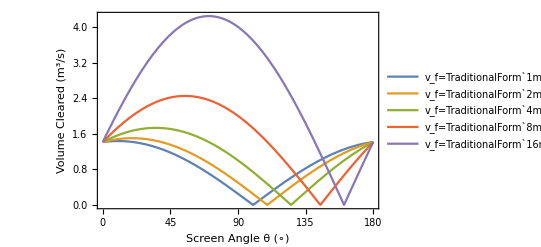

```mathematica
vfs = {1,2,4,8,16};
Plot[Evaluate[Table[hm[vf,θ*π/180]*(ds)*vf,{vf,vfs}]],{θ,0,180},

FrameTicks->{Table[i,{i,0,180,45}],Automatic,Automatic,Automatic},Frame->{True},FrameLabel->{"


Screen Angle θ (∘)","Volume Cleared (m^3/s)"},PlotLegends->Placed[Table[StringForm["v_f=``m/s",vf],{vf,vfs}],{0.86,0.65}]]
```

### Data from 1976 “Vertical Distribution of some West African mosquitos (Diptera Culicidae) over open farmland in a freshwater area of the Gambia”

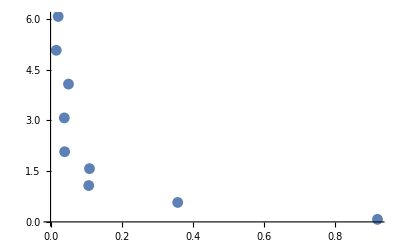

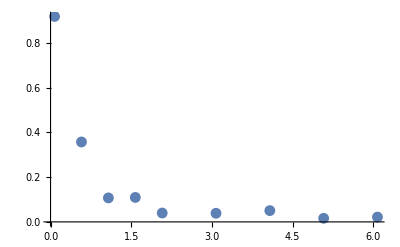

```mathematica
(*data expressed as a ratio of catch at 1m, all experiments combined*)

hINm = {0,0.5,1,1.5,2,3,4,5,6};
Aedes = {8.56,3.33,1,1.02,0.37,0.36,0.47,0.15,0.2};
MansoniaSpp = {4.59,2.03,1,0.71,0.51,0.25,0.15,0.09,0.04};
Aziemanni = {4.61,1.38,1,1.14,0.64,0.52,0.24,0.09,0.07};
Apharoensis= {5.02,1.84,1,0.83,0.67,0.42,0.54,0.21,0.14};
ASquamosus= {5.17,1.94,1,0.82,0.68,0.24,0.12,0,0.12};
Afunestus= {0.96,1.26,1,0.56,0.5,0.25,0.16,0.12,0.07};
Agambiae= {0,1.52,1,0,0.63,0.62,0.47,0.51,0.07};
Cneavei= {2.51,0.8,1,1.35,1.09,1.42,0.97,0.57,0.51};
Cthalassius= {0,0,1,0,0.57,0.33,0.53,0.38,1.43};
Cpoicilipes= {1.19,0.69,1,1.33,0.98,1.71,4.19,2.52,5.91};
PlotPts = ListPlot[Transpose[{ Normalize[Aedes],hINm+0.15/2}],AxesOrigin->{0,0}]
ListPlot[Transpose[{ hINm+0.15/2,Normalize[Aedes]}],AxesOrigin->{0,0}]
```

```mathematica
data = Transpose[{ Normalize[Aedes],hINm+0.15/2}]
nlm=NonlinearModelFit[data,{a Exp[-k h]},{{a,10},{k,1/10}},h]
```

{{0.917977,0.075},{0.35711,0.575},{0.10724,1.075},{0.109385,1.575},{0.0396789,2.075},{0.0386065,3.075},{0.050403,4.075},{0.0160861,5.075},{0.0214481,6.075}}

FittedModel[7.02462 ⅇ^(-16.7521 h)]

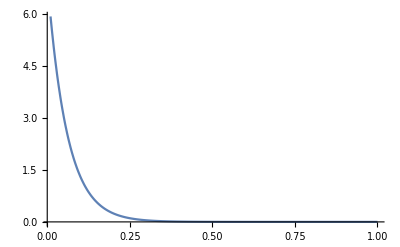

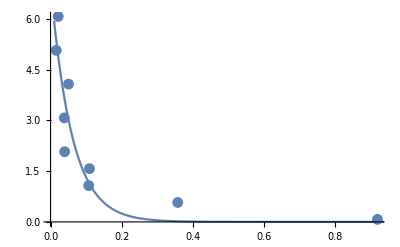

```mathematica
PlotFit = Plot[7.0246241160997736 ⅇ^(-16.752142234943413 h), {h,0.01,1},PlotRange->All,AxesOrigin->{0,0}]
Show[{PlotPts,PlotFit}]
```

```mathematica
r = 1;
Manipulate[
Module[{
w = 0.1(*width of robot,*),
ws = 0.05,(* screen is s*s*),
h = 2 (*distance screen is below the quadcopter*)
},
Graphics[{
{Black, Rectangle[{-r,-w/2},{r,w/2}],
White,Text["Quadcopter",{0,0}]
},
{(*screen*)
Rotate[{Yellow,EdgeForm[Black], Rectangle[{-s/2,-ws/2-h},{s/2,ws/2-h}],Black,Text["Screen",{0,-h}]},-θ]
}

}]], {θ,0,π/2},{{s,1.5},0.1, 2 r}]
```